# Project report

## Manifold cooling mitigation

D Malan

Department of Chemistry
University of Pretoria

20 January 2020

## Introduction

As discussed in the previous report, it seems possible that a cold spot in the inlet-end manifold spoiled some chromatograms by trapping analytes. This report discusses experiments I did to study mitigation of that problem.

## Experimental

I did a few simulated runs and varied some of the relevant instrumental settings. From the recorded data one can form an idea of the effect each setting has, and which approach would be best.

## Results

First I kept the temperature setpoint unchanged, and opened the metering valve to different settings.

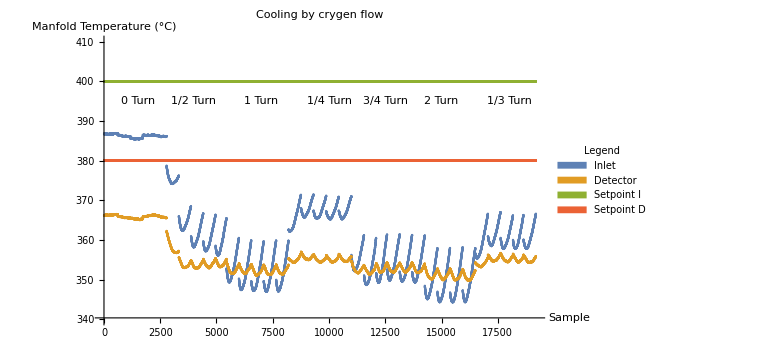

```mathematica
"2020_01_26-161750.dat"
```

Then I kept the metering valve 3/4 of a turn open and changed the setpoints.

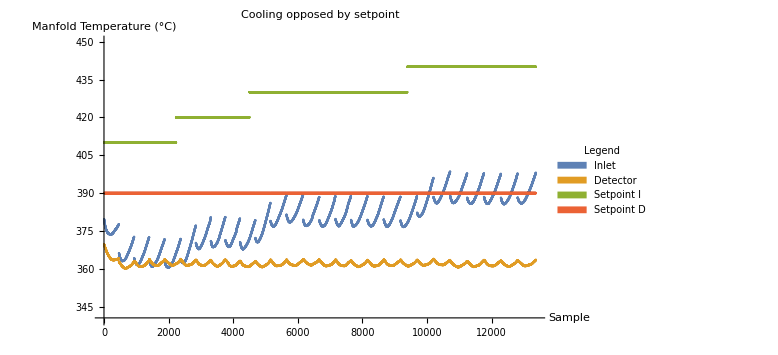

```mathematica
"2020_01_26-163504.dat"
```

Then I tried a few different controller settings of the manifold heaters.

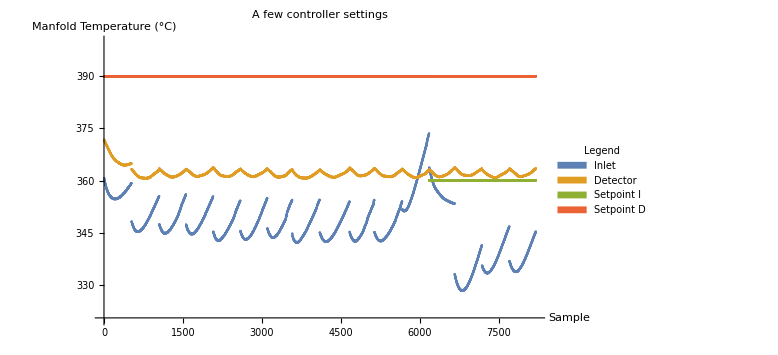

```mathematica
"2020_01_26-164729"
```

## Discussion

From the flow settings experiment it is clear that reducing the flow reduces the cooling. The minium temperature can be controlled in this way
The metering valve is a 10-turn valve, but only a quarter-turn was necessary to get adequate flow. This means that the valve is oversized for its job. A smaller valve will give more precise control. It also means that a future cryogen control system will require only a small variable orifice.

From the setpoint setting experiment one can see that, although the amount of cooling is always the same, the higher setpoint increases the minimum temperature. Higher temperature setpoints increase the risk of column damage.

Playing with the controller settings could create some changes, but nothing really made a compelling difference.

In a future design it would be possible to create a better manifold, one that does not channel the cryogen past the column that should stay hot.

For all the experiments described above, the cooling provided cooled the column  to trapping  temperatures rapidly and reliably.

## Conclusion

It is possible to keep the  inlet-end manifold temperature above a given temperature through various manipulations.

## Recommendations

Open the metering valve 1/4 turn and make the temperature setpoint  410 °C.

Replace the metering valve with a smaller one.

Use the capillary thermocouple probe to measure the actual column temperature in the manifold.